# Harmonic Oscillators

## Free Harmonic Oscillators

The governing equation of free harmonic oscillation is given by

m(d^2 x)/(ⅆ t^2)+ω^2 x=0

We solve this ordinary differential equation

```mathematica
solution=DSolve[{m*x''[t]+ω^2*x[t]==0,x[0]==x0,x'[0]==v0},x[t],t]
```

{{x[t]→(x0 ω Cos[(t ω)/(√m)]+√m v0 Sin[(t ω)/(√m)])/ω}}

And plot the solution with mass m=1 and initial conditions

ω = 2π,  x_0=1,v_0=0

over the time interval 0≤t≤5

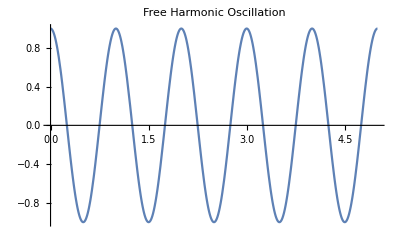

```mathematica
Plot[Evaluate[x[t]/. solution/. {m->1,ω->2*Pi,x0->1,v0->0}],{t,0,5},PlotLabel->"Free Harmonic Oscillation"]
```

## Damped Harmonic Oscillators

The governing equation of damped harmonic oscillation is given by

m(ⅆ^2 x)/(ⅆ t^2)+β ⅆx/ⅆt+ω^2 x=0

We solve this ordinary differential equation

```mathematica
solution=DSolve[{m*x''[t]+β*x'[t]+ω^2*x[t]==0,x[0]==x0,x'[0]==v0},x[t],t]
```

{{x[t]→1/(2 √(β^2-4 m ω^2))(-2 ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) m v0+2 ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) m v0-ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) x0 β+ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) x0 β+ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) x0 √(β^2-4 m ω^2)+ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) x0 √(β^2-4 m ω^2))}}

And plot the solution with mass m=1 and  initial conditions

ω = 2π,  β=1, x_0=1,v_0=0

over the time interval 0≤t≤5

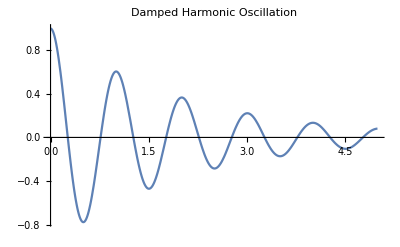

```mathematica
Plot[Evaluate[x[t]/. solution/. {m->1,ω->2*Pi,β->1,x0->1,v0->0}],{t,0,5},PlotLabel->"Damped Harmonic Oscillation"]
```

## Forced Harmonic Oscillator

The governing equation of free harmonic oscillation is given by

m(ⅆ^2 x)/(ⅆ t^2)+β ⅆx/ⅆt+ω^2 x=F_0 cos(ω_0 t)

We solve this ordinary differential equation

```mathematica
solution=DSolve[{m*x''[t]+β*x'[t]+ω^2*x[t]==F0*Cos[ω0*t],x[0]==x0,x'[0]==v0},x[t],t]
```

{{x[t]→(ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) F0 β ω^2-ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) F0 β ω^2-2 ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) m v0 ω^4+2 ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) m v0 ω^4-ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) x0 β ω^4+ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) x0 β ω^4-ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) F0 ω^2 √(β^2-4 m ω^2)-ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) F0 ω^2 √(β^2-4 m ω^2)+ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) x0 ω^4 √(β^2-4 m ω^2)+ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) x0 ω^4 √(β^2-4 m ω^2)+ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) F0 m β ω0^2-ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) F0 m β ω0^2-2 ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) m v0 β^2 ω0^2+2 ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) m v0 β^2 ω0^2-ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) x0 β^3 ω0^2+ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) x0 β^3 ω0^2+4 ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) m^2 v0 ω^2 ω0^2-4 ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) m^2 v0 ω^2 ω0^2+2 ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) m x0 β ω^2 ω0^2-2 ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) m x0 β ω^2 ω0^2+ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) F0 m √(β^2-4 m ω^2) ω0^2+ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) F0 m √(β^2-4 m ω^2) ω0^2+ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) x0 β^2 √(β^2-4 m ω^2) ω0^2+ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) x0 β^2 √(β^2-4 m ω^2) ω0^2-2 ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) m x0 ω^2 √(β^2-4 m ω^2) ω0^2-2 ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) m x0 ω^2 √(β^2-4 m ω^2) ω0^2-2 ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) m^3 v0 ω0^4+2 ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) m^3 v0 ω0^4-ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) m^2 x0 β ω0^4+ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) m^2 x0 β ω0^4+ⅇ^(1/2 t (-β/m-(√(β^2-4 m ω^2))/m)) m^2 x0 √(β^2-4 m ω^2) ω0^4+ⅇ^(1/2 t (-β/m+(√(β^2-4 m ω^2))/m)) m^2 x0 √(β^2-4 m ω^2) ω0^4+2 F0 ω^2 √(β^2-4 m ω^2) Cos[t ω0]-2 F0 m √(β^2-4 m ω^2) ω0^2 Cos[t ω0]+2 F0 β √(β^2-4 m ω^2) ω0 Sin[t ω0])/(2 √(β^2-4 m ω^2) (ω^4+β^2 ω0^2-2 m ω^2 ω0^2+m^2 ω0^4))}}

And plot the solution with mass m=1 and initial conditions

ω = ω_0=2π,  β=1, F_0=1,x_0=0,v_0=0

over the time interval 0≤t≤5

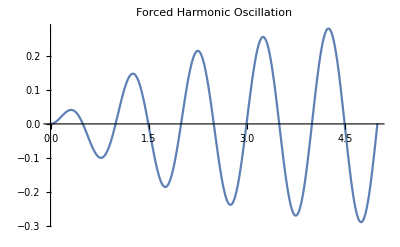

```mathematica
Plot[Evaluate[x[t]/. solution/. {m->1,ω->2*Pi,β->1,F0->2,ω0-> 2*Pi,x0->0,v0->0}],{t,0,5},PlotLabel->"Forced Harmonic Oscillation"]
```